```mathematica
<<Tableau`
<<Pseudo`
```

#### Figure 6

```mathematica
NewStateTuple[Fig6,{},{@_i[X [©_j["p"]]]⇒@_j["p"]},{},{},{}];
```

```mathematica
PrintST[Fig6]
```

<{},{@_i[X\ ©_j["p"]] ⇒ @_j["p"]},{},{},{}>

```mathematica
Tableau[TableauFig6,Fig6];
```

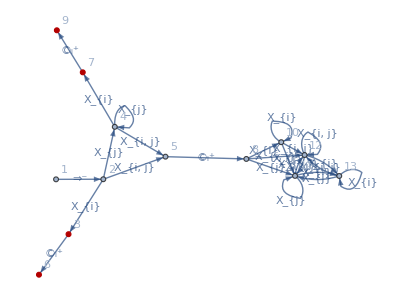

1→<{},{@_i[X\ ©_j["p"]] ⇒ @_j["p"]},{},{},{}>

2→<{@_i[X\ ©_j["p"]]},{@_j["p"]},{},{},{}>

3→<{@_i[©_j["p"]]},{@_j["p"]},{},{},{i}>

4→<{@_i[X\ ©_j["p"]]},{},{},{},{j}>

5→<{@_i[©_j["p"]]},{},{},{},{i, j}>

6→<{@_j["p"]},{@_j["p"]},{{i, j}},{},{i}>

7→<{@_i[©_j["p"]]},{},{},{},{i}>

8→<{@_j["p"]},{},{{i, j}},{},{i, j}>

9→<{@_j["p"]},{},{{i, j}},{},{i}>

10→<{@_j["p"]},{},{},{},{i}>

11→<{},{},{},{},{j}>

12→<{},{},{},{},{i, j}>

13→<{},{},{},{},{i}>

True

```mathematica
Iterate[TableauFig6]
Legend[TableauFig6]
SuccessfulQ[TableauFig6]
```

#### Figure 10

```mathematica
NewStateTuple[Fig10,{},{@_j[G [¬"p"]]⇒@_i[¬X[ ©_j["p"]]]},{},{},{}];
```

```mathematica
PrintST[Fig10]
```

<{},{@_j[G\ (! "p")] ⇒ @_i[! X\ ©_j["p"]]},{},{},{}>

```mathematica
Tableau[TableauFig10,Fig10];
```

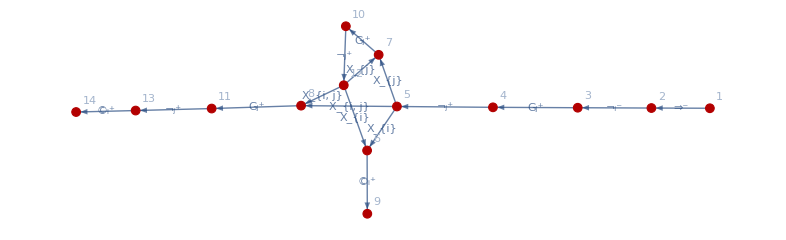

1→<{},{@_j[G\ (! "p")] ⇒ @_i[! X\ ©_j["p"]]},{},{},{}>

2→<{@_j[G\ (! "p")]},{@_i[! X\ ©_j["p"]]},{},{},{}>

3→<{@_i[X\ ©_j["p"]], @_j[G\ (! "p")]},{},{},{},{}>

4→<{@_i[X\ ©_j["p"]], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{}>

5→<{@_i[X\ ©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{}>

6→<{@_i[©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i}>

7→<{@_i[X\ ©_j["p"]], @_j[G\ (! "p")]},{},{},{},{j}>

8→<{@_i[©_j["p"]], @_j[G\ (! "p")]},{},{},{},{i, j}>

9→<{@_j["p"], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{{i, j}},{},{i}>

10→<{@_i[X\ ©_j["p"]], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{j}>

11→<{@_i[©_j["p"]], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{i, j}>

12→<{@_i[X\ ©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{j}>

13→<{@_i[©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i, j}>

14→<{@_j["p"], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{{i, j}},{},{i, j}>

False

```mathematica
Iterate[TableauFig10]
Legend[TableauFig10]
SuccessfulQ[TableauFig10]
```

#### Figure 14

```mathematica
NewStateTuple[Fig14,{@_i[F ©_j["p"]],@_j[G ¬"p"]},{},{},{},{}];
```

```mathematica
PrintST[Fig14]
```

<{@_i[F\ ©_j["p"]], @_j[G\ (! "p")]},{},{},{},{}>

```mathematica
Tableau[TableauFig14,Fig14];
```

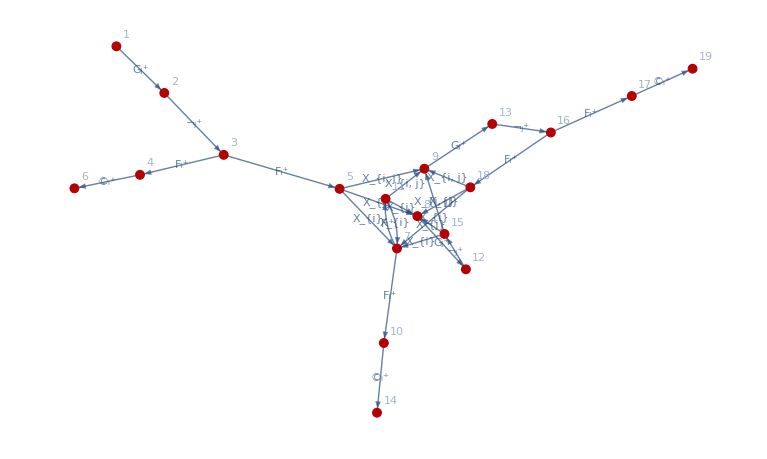

1→<{@_i[F\ ©_j["p"]], @_j[G\ (! "p")]},{},{},{},{}>

2→<{@_i[F\ ©_j["p"]], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{}>

3→<{@_i[F\ ©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{}>

4→<{@_i[©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{}>

5→<{@_i[X\ (F\ ©_j["p"])], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{}>

6→<{@_j["p"], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{{i, j}},{},{}>

7→<{@_i[F\ ©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i}>

8→<{@_i[X\ (F\ ©_j["p"])], @_j[G\ (! "p")]},{},{},{},{j}>

9→<{@_i[F\ ©_j["p"]], @_j[G\ (! "p")]},{},{},{},{i, j}>

10→<{@_i[©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i}>

11→<{@_i[X\ (F\ ©_j["p"])], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i}>

12→<{@_i[X\ (F\ ©_j["p"])], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{j}>

13→<{@_i[F\ ©_j["p"]], @_j[! "p"], @_j[X\ (G\ (! "p"))]},{},{},{},{i, j}>

14→<{@_j["p"], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{{i, j}},{},{i}>

15→<{@_i[X\ (F\ ©_j["p"])], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{j}>

16→<{@_i[F\ ©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i, j}>

17→<{@_i[©_j["p"]], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i, j}>

18→<{@_i[X\ (F\ ©_j["p"])], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{},{},{i, j}>

19→<{@_j["p"], @_j[X\ (G\ (! "p"))]},{@_j["p"]},{{i, j}},{},{i, j}>

False

```mathematica
Iterate[TableauFig14]
Legend[TableauFig14]
SuccessfulQ[TableauFig14]
```